```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;rep={kx-> k Sin[θ] Cos[ϕ],ky-> k Sin[θ]Sin[ϕ],kp-> k Sin[θ],kz-> k Cos[θ]};
ass=Assumptions->{ky,kz,κi,κr,θ,α,en,a1,a2,b1,b3,c1,c2}∈ Reals &&  k>0  && v>0 && vz>0;
(* -Graphics-;-Graphics-*)
ass={k,θ,ϕ,kx,ky,kz}∈ Reals &&  k>0;
jx=({{0, (√3)/2, 0, 0}, {(√3)/2, 0, 1, 0}, {0, 1, 0, (√3)/2}, {0, 0, (√3)/2, 0}});jy= ({{0, -(√3)/2 ⅈ, 0, 0}, {(√3)/2 ⅈ, 0, -ⅈ, 0}, {0, ⅈ, 0, -(√3)/2 ⅈ}, {0, 0, (√3)/2 ⅈ, 0}}) ; jz= ({{3/2, 0, 0, 0}, {0, 1/2, 0, 0}, {0, 0, -1/2, 0}, {0, 0, 0, -3/2}}) ;id=IdentityMatrix[4];
{σx,σy,σz}={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};id2=IdentityMatrix[2];

{nx,ny,nz}={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ] };
Jn=nx jx+ny jy+nz jz//FullSimplify;
Jn//MatrixForm;
Clear[ham,ψ,eval,en,evec,α,M];
{dx,dy,dz}={kx, ky,kz};
ham=dx jx+dy jy+dz jz;
{eval, evec}=FullSimplify[Eigensystem[ham],Assumptions->ass];
v1(*1/2*)=(kx+ⅈ ky)^2 evec[[3]]/.√(kx^2+ky^2+kz^2)->2en
v2(*3/2*)=(kx+ⅈ ky)^3 evec[[4]]/.√(kx^2+ky^2+kz^2)->2en/3
v1dag=FullSimplify[ConjugateTranspose[v1],ass]/.Conjugate[en]->en;
v2dag=FullSimplify[ConjugateTranspose[v2],ass]/.Conjugate[en]->en;
```

{-((kx-ⅈ ky) (2 en+kz)),-(kx^2+ky^2-2 kz (2 en+kz))/(√3),((kx+ⅈ ky) (2 en+3 kz))/(√3),(kx+ⅈ ky)^2}

{4 kz^2 ((2 en)/3+kz)+kx^2 ((2 en)/3+3 kz)+ky^2 ((2 en)/3+3 kz),√3 (kx+ⅈ ky) (kx^2+ky^2+2 kz ((2 en)/3+kz)),√3 (kx+ⅈ ky)^2 ((2 en)/3+kz),(kx+ⅈ ky)^3}

## wv 1

```mathematica
Clear[ψ,eq0,eq,eqn,solu,sol,κ,κr,κi,a,c1,c2];
κ=kr+ⅈ ki 0;
ψ={1,a1+ⅈ a2,b1+ⅈ b2,c1+ⅈ c2};
ψdag={1,a1-ⅈ a2,b1-ⅈ b2,c1-ⅈ c2};
prod=2FullSimplify[ψdag.(jz.ψ),ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
eq=2FullSimplify[-ⅈ ⅇ^(κ z)D[ jz.ψ ⅇ^(-κ z),z]+ky jy.ψ+kx jx.ψ -en id.ψ,ass];
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
solu=FullSimplify[Solve[eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0 && eqn[[5]]==0 && eqn[[6]]==0 && kr≠0,{kr,en,b1,b2,c1,c2}],ass]
Clear[κ,κi,en];
consis=6 (kx^2+ky^2)^2 FullSimplify[{6eq0[[1]],eqn[[7]], eqn[[8]]}/.solu,ass]
```

{a1^2+a2^2-b1^2-b2^2-3 (-1+c1^2+c2^2),0}

{-2 en+√3 (a1 kx+a2 ky),3 kr+√3 (a2 kx-a1 ky),-2 a1 en-a2 kr+√3 kx+2 b1 kx+2 b2 ky,-2 a2 en+a1 kr+2 b2 kx+√3 ky-2 b1 ky,-2 b1 en+b2 kr+2 a1 kx+√3 c1 kx-2 a2 ky+√3 c2 ky,-2 b2 en-b1 kr+2 a2 kx+√3 c2 kx+2 a1 ky-√3 c1 ky,-2 c1 en+3 c2 kr+√3 (b1 kx-b2 ky),-2 c2 en-3 c1 kr+√3 (b2 kx+b1 ky)}

{{kr→(-a2 kx+a1 ky)/(√3),en→1/2 √3 (a1 kx+a2 ky),b1→((-3+3 a1^2-a2^2) kx^2+(3+a1^2-3 a2^2) ky^2)/(2 √3 (kx^2+ky^2)),b2→(a1^2 kx ky+(-3+a2^2) kx ky+2 a1 a2 (kx^2+ky^2))/(√3 (kx^2+ky^2)),c1→(a1 (-21+9 a1^2+a2^2) kx^4-2 a2 (-3+a1^2+a2^2) kx^3 ky-4 a1 (-9+2 a1^2+6 a2^2) kx^2 ky^2-18 a2 (-3+a1^2+a2^2) kx ky^3-a1 (-9+a1^2+9 a2^2) ky^4)/(6 √3 (kx^2+ky^2)^2),c2→(a2 (-9+9 a1^2+a2^2) kx^4+18 a1 (-3+a1^2+a2^2) kx^3 ky+4 a2 (-9+6 a1^2+2 a2^2) kx^2 ky^2+2 a1 (-3+a1^2+a2^2) kx ky^3-a2 (-21+a1^2+9 a2^2) ky^4)/(6 √3 (kx^2+ky^2)^2)}}

{{-((-3+a1^2+a2^2) ((-9+9 a1^2+a2^2) kx^2+16 a1 a2 kx ky+(-9+a1^2+9 a2^2) ky^2) ((-3+9 a1^2+a2^2) kx^2+16 a1 a2 kx ky+(-3+a1^2+9 a2^2) ky^2)),-((-3+a1^2+a2^2) kx (kx^2-3 ky^2) ((-3+9 a1^2+a2^2) kx^2+16 a1 a2 kx ky+(-3+a1^2+9 a2^2) ky^2)),(-3+a1^2+a2^2) ky (-3 kx^2+ky^2) ((-3+9 a1^2+a2^2) kx^2+16 a1 a2 kx ky+(-3+a1^2+9 a2^2) ky^2)}}

```mathematica
FullSimplify[Solve[(-3+9 a1^2+a2^2) kx^2+16 a1 a2 kx ky+(-3+a1^2+9 a2^2) ky^2==0,{a1}],ass]
```

{{a1→-(8 a2 kx ky+√3 √((kx^2+ky^2) (-3 (-3+a2^2) kx^2+(1-3 a2^2) ky^2)))/(9 kx^2+ky^2)},{a1→(-8 a2 kx ky+√3 √((kx^2+ky^2) (-3 (-3+a2^2) kx^2+(1-3 a2^2) ky^2)))/(9 kx^2+ky^2)}}

```mathematica
FullSimplify[(ψ/.solu[[1]])/.{a1->Cos[α]/√3,a2->Sin[α]/√3},ass]
```

{1,ⅇ^(ⅈ α)/(√3),(4+ⅇ^(2 ⅈ α)-(8 kx)/(kx-ⅈ ky))/(3 √3),(ⅇ^(3 ⅈ α) (kx-ⅈ ky)^2-8 ⅇ^(-ⅈ α) (kx+ⅈ ky)^2-20 ⅇ^(ⅈ α) (kx^2+ky^2))/(27 (kx-ⅈ ky)^2)}

## wv 2

```mathematica
Clear[ψ,eq0,eq,eqn,solu,sol,κ,κr,κi,a,c1,c2];
κ=kr+ⅈ ki 0;
ψ={a1+ⅈ a2,1,b1+ⅈ b2,c1+ⅈ c2};
ψdag={a1-ⅈ a2,1,b1-ⅈ b2,c1-ⅈ c2};
prod=2FullSimplify[ψdag.(jz.ψ),ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
eq=2FullSimplify[-ⅈ ⅇ^(κ z)D[ jz.ψ ⅇ^(-κ z),z]+ky jy.ψ+kx jx.ψ -en id.ψ,ass];
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
solu=FullSimplify[Solve[(*eq0[[1]]==0 &&*) eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0 && eqn[[5]]==0 && eqn[[6]]==0 (*&& eqn[[7]]==0 && eqn[[8]]==0 *)&& kr≠0,{kr,en,b1,b2,c1,c2}],ass]
(*sol[kx_,ky_]={en}/.solu*)
Clear[κ,κi,en];
consis=6 (kx^2+ky^2)^2 FullSimplify[{6(a1^2+a2^2)^4 eq0[[1]],(a1^2+a2^2)^3 eqn[[7]], (a1^2+a2^2)^3 eqn[[8]]}/.solu,ass]
```

{1+3 a1^2+3 a2^2-b1^2-b2^2-3 c1^2-3 c2^2,0}

{-2 a1 en-3 a2 kr+√3 kx,-2 a2 en+3 a1 kr-√3 ky,-2 en+√3 a1 kx+2 b1 kx-√3 a2 ky+2 b2 ky,kr+√3 a2 kx+2 b2 kx+√3 a1 ky-2 b1 ky,-2 b1 en+b2 kr+2 kx+√3 c1 kx+√3 c2 ky,-2 b2 en-b1 kr+√3 c2 kx+2 ky-√3 c1 ky,-2 c1 en+3 c2 kr+√3 (b1 kx-b2 ky),-2 c2 en-3 c1 kr+√3 (b2 kx+b1 ky)}

{{kr→(a2 kx+a1 ky)/(√3 (a1^2+a2^2)),en→(√3 (a1 kx-a2 ky))/(2 (a1^2+a2^2)),b1→(-3 a1 (-1+a1^2+a2^2) kx^2+2 a2 (-1+3 a1^2+3 a2^2) kx ky+a1 (1+3 a1^2+3 a2^2) ky^2)/(2 √3 (a1^2+a2^2) (kx^2+ky^2)),b2→(-a2 (1+3 a1^2+3 a2^2) kx^2-2 a1 (-1+3 a1^2+3 a2^2) kx ky+3 a2 (-1+a1^2+a2^2) ky^2)/(2 √3 (a1^2+a2^2) (kx^2+ky^2)),c1→1/(6 √3 (a1^2+a2^2)^2 (kx^2+ky^2)^2)((-21 a1^4+a2^2-9 a2^4+a1^2 (9-30 a2^2)) kx^4+16 a1 a2 (-1+3 a1^2+3 a2^2) kx^3 ky+4 (a1-a2) (a1+a2) (-2+9 a1^2+9 a2^2) kx^2 ky^2-16 a1 a2 (-1+3 a1^2+3 a2^2) kx ky^3+(9 a1^4-9 a2^2+21 a2^4+a1^2 (-1+30 a2^2)) ky^4),c2→1/(3 √3 (a1^2+a2^2)^2 (kx^2+ky^2)^2)(-6 a1 a2 (a1^2+a2^2) kx^4-(9 a1^2+a2^2) (-1+3 a1^2+3 a2^2) kx^3 ky+4 a1 a2 (-4+9 a1^2+9 a2^2) kx^2 ky^2-(-1+3 a1^2+3 a2^2) (a1^2+9 a2^2) kx ky^3-6 a1 a2 (a1^2+a2^2) ky^4)}}

{{(-1+3 a1^2+3 a2^2) ((-a2^2+3 (a1^4+a2^4+a1^2 (-3+2 a2^2))) kx^2+16 a1 a2 kx ky+(3 a1^4+3 a2^2 (-3+a2^2)+a1^2 (-1+6 a2^2)) ky^2) ((-a2^2+9 ((-1+a1) a1+a2^2) (a1+a1^2+a2^2)) kx^2+16 a1 a2 kx ky+(9 a1^4+9 a2^2 (-1+a2^2)+a1^2 (-1+18 a2^2)) ky^2),-((-1+3 a1^2+3 a2^2) ((-a2^2+3 (a1^4+a2^4+a1^2 (-3+2 a2^2))) kx^2+16 a1 a2 kx ky+(3 a1^4+3 a2^2 (-3+a2^2)+a1^2 (-1+6 a2^2)) ky^2) (a2 ky (-3 kx^2+ky^2)+a1 (kx^3-3 kx ky^2))),-((-1+3 a1^2+3 a2^2) ((-a2^2+3 (a1^4+a2^4+a1^2 (-3+2 a2^2))) kx^2+16 a1 a2 kx ky+(3 a1^4+3 a2^2 (-3+a2^2)+a1^2 (-1+6 a2^2)) ky^2) (a2 kx^3+3 a1 kx^2 ky-3 a2 kx ky^2-a1 ky^3))}}

```mathematica
FullSimplify[Solve[(-3+9 a1^2+a2^2) kx^2+16 a1 a2 kx ky+(-3+a1^2+9 a2^2) ky^2==0,{a1}],ass]
```

{{a1→-(8 a2 kx ky+√3 √((kx^2+ky^2) (-3 (-3+a2^2) kx^2+(1-3 a2^2) ky^2)))/(9 kx^2+ky^2)},{a1→(-8 a2 kx ky+√3 √((kx^2+ky^2) (-3 (-3+a2^2) kx^2+(1-3 a2^2) ky^2)))/(9 kx^2+ky^2)}}

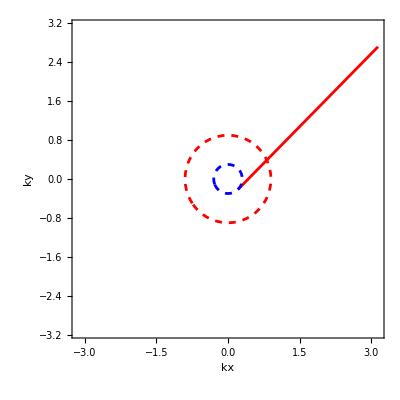

```mathematica
lim=π;mu=0.45;th=π/4;{a1,a2}={Cos[th],Sin[th]}/√3;
ar1=Quiet[ContourPlot[(√3 (a1 kx-a2 ky))/(2 (a1^2+a2^2))==mu,{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},ContourStyle->Red,RegionFunction->Function[{kx,ky,z},a2 kx+a1 ky>0 ],PlotLegends->Automatic]];

fs=ContourPlot[{ky^2+kx^2==4mu^2,ky^2+kx^2==4mu^2/9},{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},Contours->20,ContourStyle->{Directive[Red,Dashed],Directive[Blue,Dashed]}];
Show[ar1,fs]
Clear[a2,a1];
```

## plots

{√(3/2),√(3/2)}

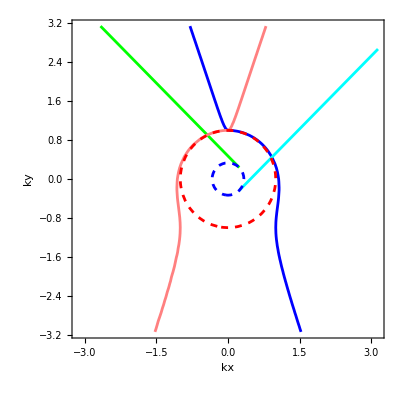

```mathematica
lim=π;mu=0.5;k0=0.5;th=π/4;{a1,a2}=√3{Cos[th],Sin[th]}
ar1=Quiet[ContourPlot[1/2 √3 (a1 kx+a2 ky)==mu,{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},ContourStyle->Green,RegionFunction->Function[{kx,ky,z},-a2 kx+a1 ky>0 ],PlotLegends->Automatic]];
(*******************)

a2= 1/√3;a1=(-8 a2 kx ky+√(3(kx^2+ky^2)) √(3 (3-a2^2) kx^2+(1-3 a2^2) ky^2))/(9 kx^2+ky^2);
ar2=Quiet[ContourPlot[1/2 √3 (a1 kx+a2 ky)==mu,{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},ContourStyle->Blue,RegionFunction->Function[{kx,ky,z},-a2 kx+a1 ky>0 && 3 (3-a2^2) kx^2+(1-3 a2^2) ky^2],PlotLegends->Automatic]];
(**************)
a1=(-8 a2 kx ky-√(3(kx^2+ky^2)) √(3 (3-a2^2) kx^2+(1-3 a2^2) ky^2))/(9 kx^2+ky^2);
ar3=Quiet[ContourPlot[1/2 √3 (a1 kx+a2 ky)==mu,{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},ContourStyle->Pink,RegionFunction->Function[{kx,ky,z},-a2 kx+a1 ky>0  && 3 (3-a2^2) kx^2+(1-3 a2^2) ky^2>=0],PlotLegends->Automatic]];

{a1,a2}={Cos[th],Sin[th]}/√3;
ar4=Quiet[ContourPlot[(√3 (a1 kx-a2 ky))/(2 (a1^2+a2^2))==mu,{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},ContourStyle->Cyan,RegionFunction->Function[{kx,ky,z},a2 kx+a1 ky>0 ],PlotLegends->Automatic]];
fs=ContourPlot[{ky^2+kx^2==4mu^2,ky^2+kx^2==4mu^2/9},{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},Contours->20,ContourStyle->{Directive[Red,Dashed],Directive[Blue,Dashed]}];
Show[ar1,ar2,ar3,ar4,fs]
Clear[a2,a1];
```